```mathematica
h[q_,z_]:=∑_(n=0)^50 q^(n^2) z^n
```

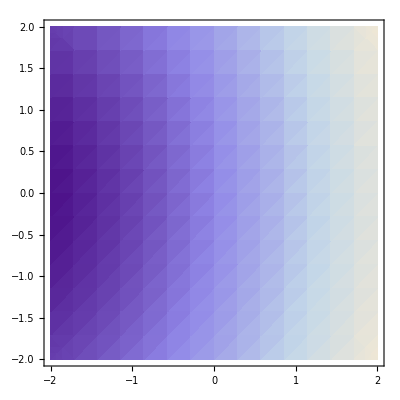

```mathematica
DensityPlot[Abs[h[0.5,x+ⅈ y]],{x,-2,2},{y,-2,2}]
```

```mathematica
∑_(n=-∞)^∞ q^(n^2)
```

EllipticTheta[3,0,q]

```mathematica
Series[EllipticTheta[3,ⅈ Log[ⅈ √-z],q],{q,0,10}]//TrigToExp
```

1+(1/z+z) q+(1/z^2+z^2) q^4+(1/z^3+z^3) q^9+O[q]^11

```mathematica
Series[EllipticTheta[3,ⅈ Log[ⅈ √(-((u^n-√(u^(2n)-4))/2)^(1/n))],q],{q,0,10}]//TrigToExp//FullSimplify
```

1+(2^(1/n) (u^n-√(-4+u^(2 n)))^(-1/n)+2^(-1/n) (u^n-√(-4+u^(2 n)))^(1/n)) q+(4^(1/n) (u^n-√(-4+u^(2 n)))^(-2/n)+4^(-1/n) (u^n-√(-4+u^(2 n)))^(2/n)) q^4+(8^(1/n) (u^n-√(-4+u^(2 n)))^(-3/n)+8^(-1/n) (u^n-√(-4+u^(2 n)))^(3/n)) q^9+O[q]^11

```mathematica
((u^n-√(u^(2n)-4))/2)^(1/n)+1/((u^n-√(u^(2n)-4))/2)^(1/n)//FullSimplify
```

2^(1/n) (u^n-√(-4+u^(2 n)))^(-1/n)+2^(-1/n) (u^n-√(-4+u^(2 n)))^(1/n)

```mathematica
CoefficientList[Series[√(1-4x)/2,{x,0,100}],x]
```

{1/2,-1,-1,-2,-5,-14,-42,-132,-429,-1430,-4862,-16796,-58786,-208012,-742900,-2674440,-9694845,-35357670,-129644790,-477638700,-1767263190,-6564120420,-24466267020,-91482563640,-343059613650,-1289904147324,-4861946401452,-18367353072152,-69533550916004,-263747951750360,-1002242216651368,-3814986502092304,-14544636039226909,-55534064877048198,-212336130412243110,-812944042149730764,-3116285494907301262,-11959798385860453492,-45950804324621742364,-176733862787006701400,-680425371729975800390,-2622127042276492108820,-10113918591637898134020,-39044429911904443959240,-150853479205085351660700,-583300119592996693088040,-2257117854077248073253720,-8740328711533173390046320,-33868773757191046886429490,-131327898242169365477991900,-509552245179617138054608572,-1978261657756160653623774456,-7684785670514316385230816156,-29869166945772625950142417512,-116157871455782434250553845880,-451959718027953471447609509424,-1759414616608818870992479875972,-6852456927844873497549658464312,-26700952856774851904245220912664,-104088460289122304033498318812080,-405944995127576985730643443367112,-1583850964596120042686772779038896,-6182127958584855650487080847216336,-24139737743045626825711458546273312,-94295850558771979787935384946380125,-368479169875816659479009042713546950,-1440418573150919668872489894243865350,-5632681584560312734993915705849145100,-22033725021956517463358552614056949950,-86218923998960285726185640663701108500,-337485502510215975556783793455058624700,-1321422108420282270489942177190229544600,-5175569924646105559418940193995065716350,-20276890389709399862928998568254641025700,-79463489365077377841208237632349268884500,-311496878311103321137536291518809134027240,-1221395654430378811828760722007962130791020,-4790408930363303911328386208394864461024520,-18793142726809884575211361279087545193250040,-73745243611532458459690151854647329239335600,-289450081175264899454283846029490767264392230,-1136359577947336271931632877004667456667613940,-4462290049988320482463241297506133183499654740,-17526585015616776834735140517915655636396234280,-68854441132780194707888052034668647142985206100,-270557451039395118028642463289168566420671280440,-1063353702922273835973036658043476458723103404520,-4180080073556524734514695828170907458428751314320,-16435314834665426797069144960762886143367590394940,-64633260585762914370496637486146181462681535261000,-254224158304000796523953440778841647086547372026600,-1000134600800354781929399250536541864362461089950800,-3935312233584004685417853572763349509774031680023800,-15487357822491889407128326963778343232013931127835600,-60960876535340415751462563580829648891969728907438000,-239993345518077005168915776623476723006280827488229600,-944973797977428207852605870454939596837230758234904050,-3721443204405954385563870541379246659709506697378694300,-14657929356129575437016877846657032761712954950899755100,-57743358069601357782187700608042856334020731624756611000,-227508830794229349661819540395688853956041682601541047340}

```mathematica
Mod[CoefficientList[Series[√(1-4x)/2,{x,0,100}],x],2]
```

{1/2,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
CoefficientList[Series[(1-3x+x^2)/(1+x+x^2+x^3),{x,0,100}],x]
```

{1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1,-4,4,-1,1}

```mathematica
Mod[CoefficientList[Series[(1-3x)/(1+x),{x,0,100}],x],2]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Mod[Table[(1/2)(-1)^n+(-3)^n √π Hypergeometric2F1[3/2,-n,3/2-n,-1/3]/(4 n! Gamma[3/2-n]),{n,100}],2]
```

{0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1,1,0,0,1,0}